## Class 1

```mathematica
List[a,b,cc]
```

{a,b,cc}

```mathematica
2+2
```

4

```mathematica
N[Sqrt[2],80]
```

1.414213562373095048801688724209698078569671875376948073176679737990732478462107

```mathematica
(3+2i) + (1+5/2i)
```

4+(9 i)/2

```mathematica
Solve[x-5==81,x]
```

{{x→86}}

```mathematica
Min[1,1,2-5,2]
```

-3

```mathematica
RandomInteger[{-8,2},{3,2,6}]
```

{{{-2,-3,-6,-3,0,-7},{1,-5,-7,2,-1,-5}},{{-2,-6,-4,-7,-7,-7},{-5,0,-7,-1,-6,-7}},{{2,-3,-1,1,-3,-5},{0,-3,-7,-1,-7,-5}}}

```mathematica
data = ExampleData[{"Geometry3D","StanfordBunny","VertexData"}];
```

ExampleData::notcoll: {"Geometry3D", "StanfordBunny", "VertexData"} is not a known collection for ExampleData. Use ExampleData[] for a list of collections.

```mathematica
Join[{3,3,2},{x,{45}}]
```

{3,3,2,x,{45}}

```mathematica
pts = Flatten[Table[{x,y,0},{x,0,5,1},{y,0,5,1}],1]
```

{{0,0,0},{0,1,0},{0,2,0},{0,3,0},{0,4,0},{0,5,0},{1,0,0},{1,1,0},{1,2,0},{1,3,0},{1,4,0},{1,5,0},{2,0,0},{2,1,0},{2,2,0},{2,3,0},{2,4,0},{2,5,0},{3,0,0},{3,1,0},{3,2,0},{3,3,0},{3,4,0},{3,5,0},{4,0,0},{4,1,0},{4,2,0},{4,3,0},{4,4,0},{4,5,0},{5,0,0},{5,1,0},{5,2,0},{5,3,0},{5,4,0},{5,5,0}}

```mathematica
Graphics3D[
{PointSize@0.1, Red, Sphere[#,0.2] & /@pts},
ImageSize->256
]
```

-Graphics3D-

## Class 2

```mathematica
StringTake["hahahah sdsd, sds.",{5,10}]
```

hah sd

```mathematica
str = "hahahah sdsd, sds."
```

hahahah sdsd, sds.

```mathematica
Characters[str]
```

{h,a,h,a,h,a,h, ,s,d,s,d,,, ,s,d,s,.}

```mathematica
Sort@%
```

{.,,, , ,a,a,a,d,d,d,h,h,h,h,s,s,s,s}

```mathematica
list1 = {2,d,ddd,33,{asd,d,100},{ "as",{20,s}}}
TreeForm@list1
```

{2,d,ddd,33,{asd,d,100},{as,{20,s}}}

-Graphics-

```mathematica
Replace[list1,d->"ABC",All]
```

{2,ABC,ddd,d2d,{asd,ABC,100},{as,{we,s}}}

```mathematica
Replace[list1,100->"ABC",{2}]
```

{2,d,ddd,d2d,{asd,d,ABC},{as,{we,s}}}

```mathematica
Head@list1[[3]]
```

Symbol

```mathematica
Replace[list1,_String->"ABC",All]
```

{2,d,ddd,d2d,{asd,d,100},{ABC,{we,s}}}

```mathematica
Replace[list1,_Symbol->"ABC",All]
```

{2,ABC,ABC,ABC,{ABC,ABC,100},{as,{ABC,ABC}}}

```mathematica
Replace[list1,x_Integer->2x,All]
```

{4,d,ddd,66,{asd,d,200},{as,{40,s}}}

```mathematica
Cases[list1,x_Integer:>2x,All]
```

{4,66,200,40}

part 2

```mathematica
temp =RandomReal[{1},10]
```

{0.826245,0.494488,0.241644,0.318091,0.187666,0.155926,0.33764,0.138031,0.0640794,0.0268888}

```mathematica
data =(temp = RotateLeft[temp])&/@Range[3]
```

{{0.138031,0.0640794,0.0268888,0.826245,0.494488,0.241644,0.318091,0.187666,0.155926,0.33764},{0.0640794,0.0268888,0.826245,0.494488,0.241644,0.318091,0.187666,0.155926,0.33764,0.138031},{0.0268888,0.826245,0.494488,0.241644,0.318091,0.187666,0.155926,0.33764,0.138031,0.0640794}}

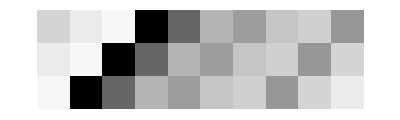

```mathematica
ArrayPlot[data,Frame->False]
```

```mathematica
Column@RandomReal[1,{4,4}]
```

{0.842345,0.0919231,0.400612,0.300238}
{0.394047,0.329713,0.183569,0.738309}
{0.0375457,0.652521,0.608342,0.319931}
{0.111411,0.753931,0.764846,0.655031}

```mathematica
data1=RandomReal[1,{4,4,3}]
```

{{{0.398266,0.286976,0.725675},{0.414468,0.951098,0.648704},{0.988599,0.175377,0.75342},{0.96017,0.627134,0.99174}},{{0.743853,0.708935,0.862017},{0.38913,0.435517,0.404264},{0.354179,0.383621,0.716031},{0.956112,0.641049,0.187186}},{{0.607047,0.911277,0.718687},{0.157935,0.764421,0.961206},{0.386688,0.994873,0.44398},{0.979981,0.984331,0.979647}},{{0.830275,0.880253,0.755951},{0.432204,0.414524,0.44418},{0.117245,0.218869,0.507941},{0.413612,0.900614,0.383109}}}

```mathematica
Image[data1]
```

-Graphics-

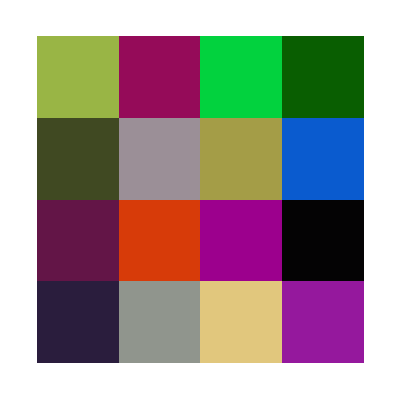

```mathematica
ArrayPlot[data1]
```

```mathematica
RGBColor@data1[[1,3]]
```

RGBColor[{0.9885990932378281, 0.17537700639846632, 0.7534203279534235}]

```mathematica
Head@-Graphics-
```

Graphics

```mathematica
ImageData[-Graphics-][[1]]
```

{{0.398266,0.286976,0.725675},{0.414468,0.951099,0.648704},{0.988599,0.175377,0.75342},{0.96017,0.627134,0.99174}}

```mathematica
ImageAdd[-Graphics-.-Graphics-]
```

ImageAdd::imginv: Expecting an image or graphics instead of ….

ImageAdd[-Graphics-.-Graphics-]

```mathematica
ImageAdd[-Graphics-,.5]
```

-Graphics-

```mathematica
ImageAdd[-Graphics-,-Graphics-]
```

-Graphics-

```mathematica
{{1,2,3},{1,12,33}}+66
```

{{67,68,69},{67,78,99}}

```mathematica
{{1,2,3},{1,12,33}}+{{1,2,3},{1,12,-Graphics-}}
```

{{2,4,6},{2,24,-Graphics-}}

```mathematica
img = -Graphics-;
```

```mathematica
imgD = ImageData@img;
```

```mathematica
ImageDimensions@img
```

{442,288}

```mathematica
ColorSeparate@img
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Image@Replace[imgD,{r_,g_,b_}:>{r,1,b},All]
```

-Graphics-

```mathematica
notes = {
SoundNote[{"C","G","B"},1,"Guitar"]
}
```

{SoundNote[{C,G,B},1,Guitar]}

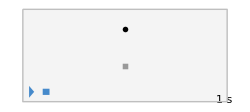

```mathematica
Sound@notes
```

```mathematica
d1 = Range@12;
d2=Range@6;
coords=Tuples[{d1,d2}]
```

{{1,1},{1,2},{1,3},{1,4},{1,5},{1,6},{2,1},{2,2},{2,3},{2,4},{2,5},{2,6},{3,1},{3,2},{3,3},{3,4},{3,5},{3,6},{4,1},{4,2},{4,3},{4,4},{4,5},{4,6},{5,1},{5,2},{5,3},{5,4},{5,5},{5,6},{6,1},{6,2},{6,3},{6,4},{6,5},{6,6},{7,1},{7,2},{7,3},{7,4},{7,5},{7,6},{8,1},{8,2},{8,3},{8,4},{8,5},{8,6},{9,1},{9,2},{9,3},{9,4},{9,5},{9,6},{10,1},{10,2},{10,3},{10,4},{10,5},{10,6},{11,1},{11,2},{11,3},{11,4},{11,5},{11,6},{12,1},{12,2},{12,3},{12,4},{12,5},{12,6}}

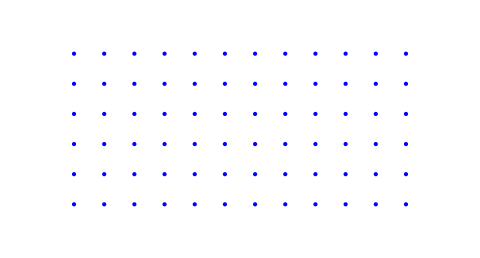

```mathematica
G1 = Graphics[{
{Blue,Point@#}&/@coords
},
ImageSize->480,
PlotRange->{{0,13},{0,7}}
]
```

```mathematica
Graphics[
{
{Red,Thickness@0.1,Circle[{0,0},1]}，
{Blue,Thickness@0.1,Circle[{1,0},1]}
},
ImageSize->256]
```

-Graphics-